Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Intro. The standard way to get an interpolating function in Mathematica is to ask for it. However, as I discuss in problem 7, there may be a better way, since the nonavailability of the equation for the interpolated function is a decided disadvantage. What I do here is to call an interpolated function, then use it to manufacture a list of 200 points, then employ the Fit command to design a function which mimics the interpolated function, giving it the assignment of developing a curve from the 200 sample points, leveraging the advantage of its 20-exponent variable span in creating the curve. I thought this was smart when I did it, but I now think it is junk.

```mathematica
data ={{0,0},{0.1,.3},{0.5,.6},{1,-.2},{2,3}}
```

{{0,0},{0.1,0.3},{0.5,0.6},{1,-0.2},{2,3}}

```mathematica
f=Interpolation[data]
```

InterpolatingFunction[{{0., 2.}}, <>]

```mathematica
datai=Table[{n,f[n]},{n,0,2,0.01}];
```

The interpolating polynomial is extremely long and cumbersome-looking. Just sticking it in here.

```mathematica
ip=InterpolatingPolynomial[datai,x];
```

```mathematica
tf=Fit[datai,{x^20,x^19,x^18,x^17,x^16,x^15,x^14,x^13,x^12,x^11,x^10,x^9,x^8,x^7,x^6,x^5,x^4,x^3,x^2,x,x^0},x]
```

0.00101515+3.22001 x+11.1129 x^2-346.654 x^3+3852.28 x^4-25880.5 x^5+114305. x^6-348455. x^7+755491. x^8-1.18323×10^6 x^9+1.33993×10^6 x^10-1.07486×10^6 x^11+569043. x^12-147155. x^13-37781.9 x^14+55021.7 x^15-25820.5 x^16+6817.26 x^17-1021.29 x^18+71.9705 x^19-0.901307 x^20

```mathematica
lm=LinearModelFit[data,{x^4,x^3,x^2,x,x^0},x];
```

```mathematica
p1=ListPlot[data,PlotStyle->Red,Filling->Bottom,ImageSize->400];
```

```mathematica
p2=Plot[lm[x],{x,0,2}, ImageSize->400,PlotStyle->{Blue,Thickness[0.002]}];
```

```mathematica
p3=Plot[f[x],{x,0,2},ImageSize->400,PlotStyle->{Orange,Thickness[0.002]}];
```

```mathematica
p4=Plot[tf,{x,0,2},ImageSize->400,PlotStyle->{Green,Thickness[0.002]}];
```

```mathematica
p5=Plot[tf,{x,0.8,1.2},ImageSize->300,PlotStyle->{Green,Thickness[0.002]}];
```

```mathematica
p6=Plot[f[x],{x,0.8,1.2},ImageSize->300,PlotStyle->{Orange,Thickness[0.002]}];
```

The blue of the unsophisticated linear model fit, lm, takes a different path than the interpolated function f, as shown on the left plot. The ornate fit function tf, with all its exponents, is not seen in the left chart, where at the presentation scale it is totally hidden by the interpolating curve f, and only peeks out in the right chart, where it emerges to smooth a visible corner in f. That visible orange corner, I believe, is evidence that the interpolation function assembles a sequence of piecewise functions to do the job, using as many as it finds necessary.

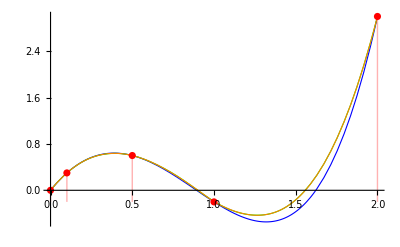
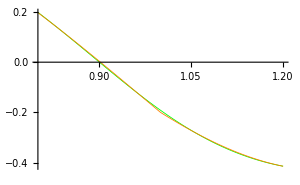

```mathematica
Row[{Show[{p2,p4,p3,p1}],Show[{p5,p6}]}]
```

1. Linear interpolation. Calculate p_1[x] in example 1 and from it Log[9.3].

```mathematica
Clear["Global`*"]
```

The real substance of problem 1 is just a log, worked out by hand according to the very similar example 1 on p. 810 and amounting to

0.4(Log[9.0]) + 0.6(Log[9.5]) =

```mathematica
.4(2.1972)+.6(2.2513)
```

2.22966

```mathematica
N[Log[9.3]-%]
```

0.0003544

The error, noted above, is not listed in the text answer.

3.  Quadratic interpolation. Gamma function. Calculate the Lagrange polynomial p_2(x) for the values Γ[1.00]=1.0000, Γ[1.02]=0.9888, Γ[1.04]=0.9784 of the gamma function ((24) in appendix A3.1) and from it approximations of Γ[1.01] and Γ[1.03].

As can be seen, I elected to use an InterpolatingPolynomial instead of a Lagrange method.

```mathematica
Clear["Global`*"]
```

```mathematica
inpp[x_]=InterpolatingPolynomial[{{1.00,1.000},{1.02,0.9888},{1.04,0.9784}},x]
```

0.9784+(-0.54+1. (-1.+x)) (-1.04+x)

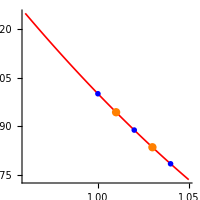

```mathematica
Plot[inpp[x],{x,0.96,1.05},ImageSize->200,PlotStyle->{Red,Thickness[0.006]},AspectRatio->1,Epilog->{{Blue,PointSize[0.02],Point[{1.00,1.000}]},{Blue,PointSize[0.02],Point[{1.02,0.9888}]},{Blue,PointSize[0.02],Point[{1.04,0.9784}]},{Orange,PointSize[0.03],Point[{1.01,0.9943}]},{Orange,PointSize[0.03],Point[{1.03,0.9835}]}}]
```

```mathematica
inpp[1.01]
```

0.9943

```mathematica
inpp[1.03]
```

0.9835

The green cells above match the answers in the text. The function plot looks almost linear in the small interval.

5.  Linear and quadratic interpolation. Find ⅇ^-0.25 and ⅇ^-0.75 by linear interpolation of ⅇ^-x with x_0=0, x_1=0.5, x_2=1 and from it ⅇ^-0.25 and ⅇ^-0.75. Compare the errors. Use 4S-values of ⅇ^-x.

```mathematica
Clear["Global`*"]
```

First look at the answers I will be looking for.

```mathematica
f[x_]=ⅇ^-x
```

ⅇ^-x

```mathematica
f[0.25]
```

0.778801

```mathematica
f[0.75]
```

0.472367

I’m only working with the three points. Just to take a look at their range,

```mathematica
Table[{x,f[x]},{x,{0,0.5,1}}]
```

{{0,1},{0.5,0.606531},{1,1/ⅇ}}

I can create the IP. Preserving values expressed in function form makes it much more accurate than pasting in the above output.

```mathematica
inpp2[x_]=InterpolatingPolynomial[{{0,1},{0.5,f[0.5]},{1,1/ⅇ}},x]
```

1/ⅇ+(-1+1/ⅇ+0.309636 x) (-1+x)

And plot it. Thankfully it is interpolation, not extrapolation, and the values sought are bracketed, so the flaky curve match should not be a problem within the interval of interest, which is 0 to 1. The text uses both linear and quadratic interpolation, with much better numbers produced by the quadratic.

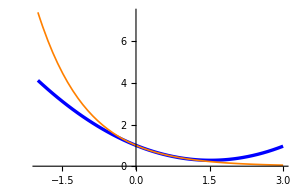

```mathematica
p1=Plot[{inpp2[x],ⅇ^-x},{x,-2,3},ImageSize->300,PlotStyle->{{Blue,Thickness[0.008]},{Orange,Thickness[0.004]}}]
```

```mathematica
inpp2[0.25]
```

0.783913

```mathematica
0.7839130646380448-0.7788007830714049
```

0.00511228

text error reported for above is 0.0245, greater than yellow. So in this case the Mathematica method is superior.

```mathematica
inpp2[0.75]
```

0.467853

```mathematica
%-0.4723665527410147
```

-0.00451377

text error for above is 0.0148, greater than yellow. Again, in posting a smaller error, the linear interpolation of the Mathematica method shows its superiority.

Supposing it is okay to recognize this as Exp, or to something resembling it, there is another way to do this with FindFit

```mathematica
Clear["Global`*"]
```

same data used in this little isolated section on experimental method of FindFit

```mathematica
data={{0,1},{0.5,0.6065306597126334},{1,1/ⅇ}};
```

a model is chosen similar to the appearance of the data,

```mathematica
model=a Exp[-k t];
```

and parameters are solved for, which might make the model usefully compliant.

```mathematica
fit=FindFit[data,model,{a,k},t]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{a→1.,k→1.}

The model is calculated, resulting in a curve function description.

```mathematica
modelf=Function[{t},Evaluate[model/.fit]]
```

Function[{t},1. ⅇ^(-1. t)]

With only trivial parameters in this case, the method does not show to advantage.

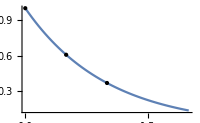

```mathematica
Plot[modelf[t],{t,0,2},Epilog->Map[Point,data],ImageSize->200]
```

If I got this far I would be able to look at Function[{t},1. ⅇ^(-1. t)] and understand that that function would put points on the curve, then define it directly.

```mathematica
m[t_]=Exp[-t]
```

ⅇ^-t

```mathematica
m[0.25]
```

0.778801

```mathematica
0.7788007830714049-0.7788007830714049
```

0.

In the scenario imagined, there would be no error with FindFit.

```mathematica
m[0.75]
```

0.472367

A barrel of shot fish. But the modeling part is intriguing. If I could recognize a curve, get reasonable k and a values, it might be a good way to do an interpolation. From the documentation I see that WorkingPrecision, PrecisionGoal, and AccuracyGoal are options for FindFit, unlike InterpolatingPolynomial, which could mean better performance. In problem 9 I will return to FindFit.

7.  Interpolation and extrapolation. Find the quadratic polynomial that agrees with Sin[x] at x=0, π/4, π/2, and use it for the interpolation and extrapolation of Sin[x] at x = -π/8, π/8, (3  π)/8,(5  π)/8. Compute the errors.

```mathematica
Clear["Global`*"]
```

First I try the Interpolation command in Mathematica, which works well, but has one significant drawback. I can’t get the actual equation for the curve which Mathematic creates. There are two methods of interpolating that are built in, spline and hermite. I test them both out on the problem points.

```mathematica
f=Interpolation[{{0,Sin[0]},{π/4,Sin[π/4]},{π/2,Sin[π/2]}} ,Method->"Spline"]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

Pi
InterpolatingFunction[{{0, --}}, <>]
                           2

```mathematica
g=Interpolation[{{0,Sin[0]},{π/4,Sin[π/4]},{π/2,Sin[π/2]}} ,Method->"Hermite"]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

Pi
InterpolatingFunction[{{0, --}}, <>]
                           2

I plot the results of my tests with the two methods of interpolation. There is no visible difference between them for this set of points.

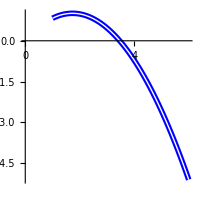

```mathematica
p1=Plot[{f[x],g[x]},{x,1,6}, ImageSize->200,PlotStyle->{{Blue,Thickness[0.02]},{White,Thickness[0.005]}},AspectRatio->1, AxesOrigin->{0,0}]
```

I put the points into a list for a linear model fit with a second order polynomial. The theory I saw on StackExchange was that the number of points indicated the necessary degree of the polynomial. With three points I would then need a cubic polynomial. But I got error messages when trying to use a cubic, and the text answer only used a square.

```mathematica
data={{0,Sin[0]},{π/4,Sin[π/4]},{π/2,Sin[π/2]}}
```

{{0,0},{π/4,1/(√2)},{π/2,1}}

So now I call for a square polynomial, and plot it. The plots of the two approaches to interpolating show different sections of the real domain, and would be a little trouble to overlay them.

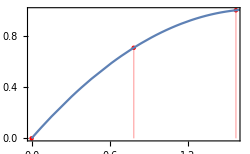

```mathematica
lm=LinearModelFit[data,{x^2,x},x];
Show[ListPlot[data,PlotStyle->Red,Filling->Bottom],Plot[lm[x],{x,0,125}],Frame->True,ImageSize->250]
```

It is easy to acquire the equation for the linear model fit polynomial, which has to be a significant advantage. Except for the first, very negligible term, the equation matches the text answer, and I’m going to go green on it.

```mathematica
Normal[lm]
```

1.54843×10^-15+1.16401 x-0.335749 x^2

Now I summarize my experience with the two forms of fitting by placing them both in a grid, along with test values. The test values require the function to act as extrapolating, as will as interpolating, functions.

```mathematica
g1={"x","Interpola","Sin[x]","Error","LinModFit","Error"};
```

```mathematica
g2=Table[{x,N[f[x]],N[Sin[x]],N[Sin[x]]-N[f[x]],lm[x],N[Sin[x]]-lm[x]},{x,{-π/8,π/8,(3 π)/8,(5 π)/8}}];
```

The interpolated function and the linear fitted polynomial, in this case, produce exactly the same results, both in terms of calculated values, and in terms of calculated errors.

```mathematica
Grid[Prepend[g2,g1],Frame->All]
```

x | Interpola | Sin[x] | Error | LinModFit | Error
-π/8 | f[-0.392699] | -0.382683 | -0.382683-f[-0.392699] | lm[-π/8] | -0.382683-lm[-π/8]
π/8 | f[0.392699] | 0.382683 | 0.382683-f[0.392699] | lm[π/8] | 0.382683-lm[π/8]
(3 π)/8 | f[1.1781] | 0.92388 | 0.92388-f[1.1781] | lm[(3 π)/8] | 0.92388-lm[(3 π)/8]
(5 π)/8 | f[1.9635] | 0.92388 | 0.92388-f[1.9635] | lm[(5 π)/8] | 0.92388-lm[(5 π)/8]

All the cells in the grid above match the corresponding numbers in the text answer.

9.  Error function (35) in appendix A3.1. Calculate the Lagrange polynomial p_2[x] for the 5S-values f[0.25] = 0.27633, f[0.5] = 0.52050, f[1.0] = 0.84270 and from p_2[x] an approximation of f[0.75] (= 0.71116).

```mathematica
Clear["Global`*"]
```

This one is kind of a disappointment. Granted, being given only three points makes it challenging for any interpolation method, but I guess what bothers me is that the text seems to do better with the three points than Mathematica does. 

I start off with the interpolating polynomial.

```mathematica
inpp[x_]=InterpolatingPolynomial[{{0.25,0.27633},{0.5,0.52050},{1.0,0.84270}},x]
```

0.8427+(0.75516-0.44304 (-0.25+x)) (-1.+x)

A plot shows the problem. On the left below, things look well, the IP is tracking the Erf function in what looks like a close manner, with just a hint of the underlying blue IP in the range of the problem values. But on the right, where a zoomed inset of the problem-specific value is shown, the IP is doing what turns out to be a poor job.

```mathematica
p1=Plot[{inpp[x],Erf[x]},{x,0,1.05},ImageSize->300,PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]}}];
```

```mathematica
p2=Plot[{inpp[x],Erf[x]},{x,0,1.05},ImageSize->200,PlotRange->{{0.745,0.755},{0.68,0.73}},PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]}},Epilog->{{Blue,PointSize[0.02],Point[{0.75,0.70929}]},{Blue,PointSize[0.02],Point[{0.75,0.71116}]}}];
```

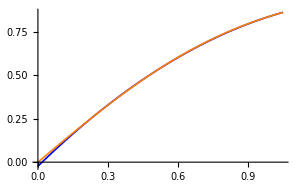
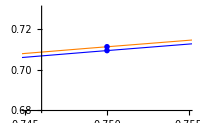

```mathematica
Row[{p1,p2}]
```

The two cells below tell the tale. Only one digit of significance agreement (or I guess two, if I rounded that far). I tried several other interpolation devices, but could not improve it much until I entered the Erf points for x = 0.7 and x = 0.8. Then I got agreement to four significant digits. Which seems pretty lame, contrived. If the interpolated function is not a known one, then it looks like I’m kind of walking in the dark.

```mathematica
inpp[0.75]
```

0.70929

```mathematica
Table[{n,Erf[n]},{n,{0.25,0.5,0.75,1.0}}]
```

{{0.25,0.276326},{0.5,0.5205},{0.75,0.711156},{1.,0.842701}}

I decided to look into this further with FindFit.

```mathematica
Clear["Global`*"]
```

Here taking the trouble to put in longer versions of the values of the model function.

```mathematica
datai={{0.25,0.27632639016823696},{0.5,0.5204998778130466},{1.0,0.8427007929497149}}
```

{{0.25,0.276326},{0.5,0.5205},{1.,0.842701}}

Here building a Interpolation function from the more precise values.

```mathematica
f=Interpolation[datai]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[{{0.25, 1.}}, <>]

Here getting the same old imprecision.

```mathematica
f[.75]
```

0.709291

Getting a solution for the sine try.

```mathematica
ffd=FindFit[datai,a Sin[b x],{a,b},x] (* using sine *)
```

{a→0.884417,b→1.26191}

Getting a solution for the parabola try.

```mathematica
ffp=FindFit[datai,a +b x+c x^2,{a,b,c},x,WorkingPrecision->20] (*using parabola *)
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (20).

{a→-0.023229117527556408795,b→1.3089860708851408511,c→-0.44305616040786954812}

Getting a solution for the exponential try.

```mathematica
ffe=FindFit[datai,a +b ⅇ^(-c x),{a,b,c},x,WorkingPrecision->20] (* using exponential *)
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (20).

{a→1.2641621447600258634,b→-1.3121809743770445164,c→1.1357178165686667905}

The exponential function

```mathematica
te[x_]=1.2641621447600258633826662088703013408502493800233056750939`20.+-1.3121809743770445164132764560080587451161751536628277667149`20.1 ⅇ^(-1.1357178165686667904505421743546779928779713927415879630267`20.x)
```

1.2641621447600258634-1.3121809743770445164 ⅇ^(-1.1357178165686667905 x)

fails to give an accurate answer.

```mathematica
te[0.75]
```

```mathematica
0.7043185020187743 (* exponential fails *)
```

```mathematica
p4=Plot[te[x],{x,0,2},PlotStyle->{Green,Thickness[0.003]}];
```

```mathematica
p1=ListPlot[datai,ImageSize->400];
```

```mathematica
tr[x_]=0.8844174815516758 Sin[1.2619134491291153 x]
```

0.884417 Sin[1.26191 x]

```mathematica
p3=Plot[tr[x],{x,0,2},PlotStyle->{Red,Thickness[0.003]}];
```

```mathematica
fp[x_]=-0.0232291175275564087954194292251486331232322306082285708689`20.+1.3089860708851408510611236124532297253618828340786412697562`20. x -0.4430561604078695481234717590268701314905913797433497845776`20. x^2
```

-0.023229117527556408795+1.3089860708851408511 x-0.44305616040786954812 x^2

```mathematica
p2=Plot[fp[x],{x,0,2},PlotStyle->{Blue,Thickness[0.003]}];
```

```mathematica
fp[0.75]
```

```mathematica
0.7092913454068726 (* parabola fails *)
```

```mathematica
tr[0.75]
```

```mathematica
0.7175603527695268 (* sine fails *)
```

Nothing I tried could produce the desired accuracy based on only three points. I also tried a double exponential, of the form a+b ⅇ^(-c x^-d) which is actually fairly close to the Erf function, but the result was even worse than any of the others.

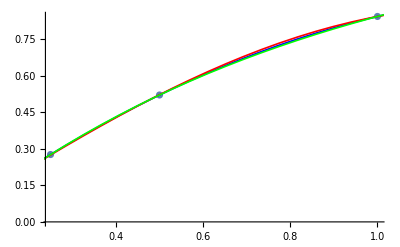

```mathematica
Show[p1,p2,p3,p4]
```

In one final stab, I add two extra points.

```mathematica
Table[{n,Erf[n]},{n,{0.0,0.25,0.5,0.8,1.0}}]
```

{{0.,0.},{0.25,0.276326},{0.5,0.5205},{0.8,0.742101},{1.,0.842701}}

```mathematica
inppe[x_]=InterpolatingPolynomial[{{0.,0.},{0.25,0.27632639016823696},{0.5,0.5204998778130466},{0.8,0.7421009647076605},{1.,0.8427007929497149}},x];
```

```mathematica
inppe[0.75]
```

0.711161

And arriving at essentially the same result which the text claims for its poly, based on three values of 5S. I think the following cells show the basic problem with this quest. The requested order cannot effectively be greater than n-1, where n is the number of points considered in interpolation. With only the three points given in the problem, the fit, a square, can’t be very good. (Note that in the first try ‘rh’, the added points are outside the span of interest.)

```mathematica
rh=Interpolation[{{0.1,Erf[0.1]},{0.25,Erf[0.25]},{0.50,Erf[0.50]},{1.0,Erf[1.0]},{1.5,Erf[1.5]}},Method->Spline,InterpolationOrder->5]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {4}.

InterpolatingFunction[{{0.1, 1.5}}, <>]

```mathematica
rh[0.75]
```

0.711623

Compare with

```mathematica
rh3=Interpolation[{{0.25,Erf[0.25]},{0.50,Erf[0.50]},{1.0,Erf[1.0]}},Method->Spline,InterpolationOrder->5]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[{{0.25, 1.}}, <>]

```mathematica
rh3[0.75]
```

0.709291

which gives the familiar degree of imprecision.

11. Cubic Lagrange interpolation. Bessel function J_0. Calculate and graph L_0, L_1, L_2, L_3 with x_0 = 0, x_1 =1, x_2 =2, x_3 = 3 on common axes. Find p_3[x] for the data (0,1), (1, 0.765198), (2, 0.223891), (3, -0.260052) (values of the Bessel function J_0[x]). Find p_3 for x = 0.5, 1.5, 2.5, and compare with the 6S-exact values 0.938470, 0.511828, -0.048384.

Examples 1 and 2 in the text deal with the L_n quantities that hallmark Lagrange interpolation. A bit labor intensive for me. I will proceed using InterpolatingPolynomial, I think.

```mathematica
Clear["Global`*"]
```

```mathematica
data={{0,1},{1,0.765198},{2,0.223891},{3,-0.260052}}
```

{{0,1},{1,0.765198},{2,0.223891},{3,-0.260052}}

```mathematica
inpp[x_]=InterpolatingPolynomial[data,x]
```

-0.260052+(-3+x) (-0.420017+(-0.0926077+0.0606448 (-1+x)) x)

```mathematica
p1=Plot[inpp[x],{x,-4,4},ImageSize->200,PlotStyle->{{Blue,Thickness[0.004]}}];
```

```mathematica
gh=Table[{x,inpp[x]},{x,data}]
```

{{{0,1},{1.,0.765198}},{{1,0.765198},{0.765198,0.861319}},{{2,0.223891},{0.223891,0.992776}},{{3,-0.260052},{-0.260052,0.965931}}}

```mathematica
inpp[0.5]
```

0.943654

```mathematica
inpp[1.5]
```

0.510116

```mathematica
inpp[2.5]
```

```mathematica
-0.04799281250000004 (* text answer was -0.047991 *)
```

```mathematica
gk={{0.5,0.943654},{1.5,0.510116},{2.5,-0.0479928}}
```

{{0.5,0.943654},{1.5,0.510116},{2.5,-0.0479928}}

```mathematica
p3=ListPlot[gk];
```

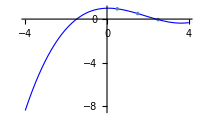

```mathematica
Show[p1,p3]
```

The curve fit looks pretty good to me.

13.  Lower degree. Find the degree of the interpolation polynomial for the data (-4, 50), (-2, 18), (0, 2), (2, 2), (4, 18), using a difference table. Find the polynomial.

```mathematica
Clear["Global`*"]
```

Needless to say, I don’t use a difference table on this one.

```mathematica
data={{-4,50},{-2,18},{0,2},{2,2},{4,18}}
```

{{-4,50},{-2,18},{0,2},{2,2},{4,18}}

```mathematica
inpp[x_]=InterpolatingPolynomial[data,x]
```

50+(4+x) (-16+2 (2+x))

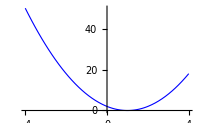

```mathematica
p1=Plot[inpp[x],{x,-4,4},ImageSize->200,PlotStyle->{{Blue,Thickness[0.004]}}]
```

I have the equation of the interpolation function, and it looks like the degree is 2. No test points here though. Working with five seeds points, it might indicate likelihood of good agreement and small errors.

15. Divided differences. Obtain p_2 in example 2 from numbered line (10), p. 814.

There is a notebook with specific code of NDD at http://nm.mathforcollege.com/topics/newton_divided_difference_method.html, but since it is from 2002, I would be surprised if it worked out of the box. It does look specific though. There is a very modern but maybe too extensive SEMma discussion at http://nm.mathforcollege.com/topics/newton_divided_difference_method.html. I don’t currently have the necessary curiosity to delve into how NDD can be used in Mathematica.

17.  Backward difference formula (18). Use p_2[x] in numbered line (18), p. 818, and the values of erf x, x = 0.2, 0.4, 0.6 in table A4 of appendix 5, compute erf[0.3] and the error. (4S-exact erf[0.3] = 0.3286).

I will avoid the backward difference and just go with InterpolatingPolynomial.

```mathematica
Clear["Global`*"]
```

```mathematica
Table[{x,Erf[x]},{x,{0.2,0.4,0.6}}]
```

{{0.2,0.222703},{0.4,0.428392},{0.6,0.603856}}

```mathematica
data={{0.2,0.22270258921047847},{0.4,0.42839235504666856},{0.6,0.603856090847926}}
```

{{0.2,0.222703},{0.4,0.428392},{0.6,0.603856}}

```mathematica
inpp[x_]=InterpolatingPolynomial[data,x]
```

0.603856+(0.952884-0.377825 (-0.2+x)) (-0.6+x)

```mathematica
va=inpp[0.3]
```

0.329326

```mathematica
vb=Erf[0.3]
```

0.328627

with an error the size of

```mathematica
vb-va
```

-0.000698966

Mathematica’s InterpolatingPolynomial came up with the same answer as the text.

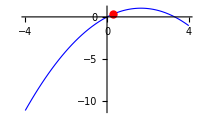

```mathematica
p1=Plot[inpp[x],{x,-4,4},ImageSize->200,PlotStyle->{{Blue,Thickness[0.004]}},Epilog->{Red,PointSize[0.03],Point[{0.3,0.329326}]}]
```

This problem dealt with interpolation of the Erf function , the same as in problem 9. There the Efr function was an embarrassing incident, but here it gives less trouble, with a reassuringly small error.

General comments on Interpolation.
1. My go-to method is InterpolatingPolynomial. (as in problem 17).
2. If IP seems to fall short, FindFit should be looked at. (as discussed in problems 5 and 9).
3. If these two approaches don’t work, a custom Fit function, (using the method described in the Intro), may be worth a try.